```mathematica
(* expand the binomial in Cos[ω]^L and integrate term by term analytically 
pick the s- term  (E^(I ω s) E^(-I ω (L-s)))Binomial[L,s]
*)
```

```mathematica
HH =Expand[E^(I ω q)TrigToExp[Cos[ω]^(-2+N) Sin[ω]^2]/.(ⅇ^(-ⅈ ω)+ⅇ^(ⅈ ω))^L_ :> Binomial[L,s]E^( I ω s - I ω(L-s))]
```

2^(1-N) ⅇ^(ⅈ q ω-ⅈ (-2+N-s) ω+ⅈ s ω) Binomial[-2+N,s]-2^-N ⅇ^(-2 ⅈ ω+ⅈ q ω-ⅈ (-2+N-s) ω+ⅈ s ω) Binomial[-2+N,s]-2^-N ⅇ^(2 ⅈ ω+ⅈ q ω-ⅈ (-2+N-s) ω+ⅈ s ω) Binomial[-2+N,s]

```mathematica
ClearAll[subInt];
```

```mathematica
subInt[ s_] = {E^(X_) F_:> (F/.Solve[D[X,ω]==0,s][[1]])}
```

{ⅇ^X_ F_:>(F/.Solve[∂_ω X==0,s]⟦1⟧)}

```mathematica
(* 
this substitution is equivalent to integration over ω -- selection of the constant term in binomial expansion
*)
```

```mathematica
JJ[q_] =FullSimplify[HH/.subInt[s]]
```

-2^-N (Binomial[-2+N,1/2 (-4+N-q)]-2 Binomial[-2+N,1/2 (-2+N-q)]+Binomial[-2+N,(N-q)/2])

```mathematica
1/4 Cot[ Pi p/q]^2((Binomial[-2+N,1/2 (-2+N-q)] FullSimplify[(JJ[q]/Binomial[-2+N,1/2 (-2+N-q)]  )])/.q ->q r)
```

(2^-N (N-q^2 r^2) Binomial[-2+N,1/2 (-2+N-q r)] Cot[(p π)/q]^2)/(N^2-q^2 r^2)

```mathematica
(2^-N (N-q^2 r^2) Binomial[-2+N,1/2 (-2+N-q r)] Cot[(p π)/q]^2)/(N^2-q^2 r^2)(N(N-1)/2)/4//FullSimplify
```

(2^(-5-N) (N-q^2 r^2) Cot[(p π)/q]^2 Gamma[1+N])/(Gamma[1/2 (2+N-q r)] Gamma[1/2 (2+N+q r)])

```mathematica
asymp =Normal[Series[(2^(-5-N) (N-N z^2 )  Gamma[1+N])/(Gamma[1/2 (2+N-z Sqrt[N])] Gamma[1/2 (2+N+z Sqrt[N] )]),{N, Infinity,2}]]
```

-(ⅇ^(-z^2/2) √N (-1+z^2))/(16 √(2 π))+(ⅇ^(-z^2/2) (-1+z^2) (3-6 z^2+z^4))/(192 √N √(2 π))-(ⅇ^(-z^2/2) (-45+705 z^2-1230 z^4+678 z^6-113 z^8+5 z^10))/(23040 N^(3/2) √(2 π))

```mathematica
Integrate[asymp,{z,-Infinity,Infinity}]
```

0

```mathematica
(√N)/(64 √π) 1/3 2 Zeta[2]/(3 Zeta[3])
```

(√N π^(3/2))/(1728 Zeta[3])

```mathematica
IIodd[M_?OddQ, q_?OddQ] :=2Sum[2^(-5-M) (M-s^2)Binomial[M,(M+s)/2] ,{s,q, M,2q}]//Quiet;
```

```mathematica
testprime =With[{MM=101},ParallelTable[{q,IIodd[MM,q]},{q,3,MM-1,2}]];
```

```mathematica
Max[N[testprime]]
```

99.

```mathematica
Min[N[testprime]]
```

-0.224218

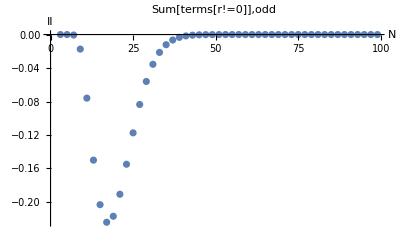

```mathematica
ListPlot[testprime, PlotLabel->"Sum[terms[r!=0]],odd",
AxesLabel->{N,II}]
```

```mathematica
IIeven[M_, q_?EvenQ] :=2Sum[2^(-5-M) (M-s^2)Binomial[M,(M+s)/2] ,{s,q, M,q}]//Quiet;
```

```mathematica
IIeven[M_, q_?OddQ] :=2Sum[2^(-5-M) (M-s^2)Binomial[M,(M+s)/2] ,{s,2q, M,2q}]//Quiet;
```

```mathematica
Normal[Series[(2^(-5-N) (N-qr^2 )  Gamma[1+N])/(Gamma[1/2 (2+N-qr)] Gamma[1/2 (2+N+qr )]),{N, Infinity,2}]]
```

(√N)/(16 √(2 π))-(1+6 qr^2)/(64 √N √(2 π))+(1+28 qr^2+20 qr^4)/(512 N^(3/2) √(2 π))

```mathematica
test1 =ParallelTable[{M,II[M,M/2]},{M,100000,150000}];
```

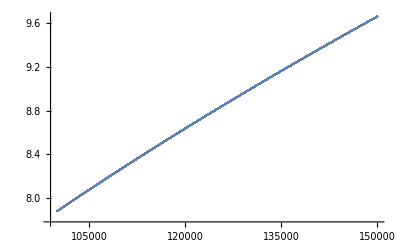

```mathematica
ListPlot[test1]
```

```mathematica
lmm = LinearModelFit[test1,{x, x^2}, x]
```

```mathematica
ShowFitLogModel[data_, model_,Ylabel_, title_]:=
Show[
ListPlot[data, PlotStyle->{Red, PointSize[0.01]},PlotLegends->{"data"}],
Plot[Exp[model[Log[x]]],{x,data[[1,1]],data[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{N[Exp[model[Log[N]]],7]},PlotRange->All],
PlotLabel->title,
AxesLabel->{"N", Ylabel}
];
```

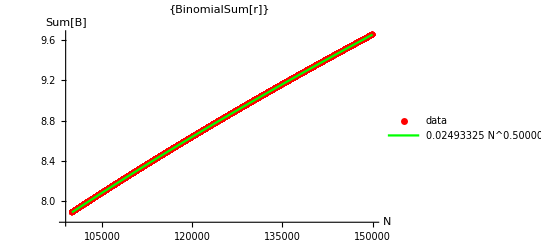

```mathematica
ShowFitLogModel[test1, loglmm,"Sum[B]", {"BinomialSum[r]"}]
```

```mathematica
lognlmm = NonlinearModelFit[Log[test1],{a + 1/2 x},{a}, x]
```

FittedModel[-3.6915292827711146537+«1»]

```mathematica
Normal[lognlmm]
```

-3.6915292827711146537+x/2

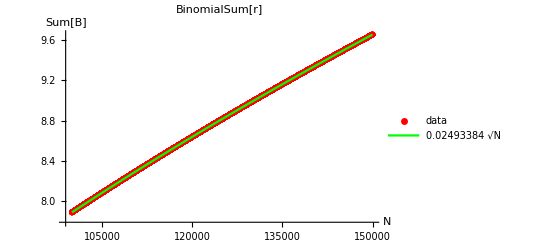

```mathematica
ShowFitLogModel[test1, lognlmm,"Sum[B]",  "BinomialSum[r]"]
```

```mathematica
N[lognlmm["ParameterTable"],7]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -3.691529 | 1.064145×10^-9 | -3.46901×10^9 | 3.355432×10^-359539

```mathematica
W0[M] :=2^(-M)Binomial[M,M/2];
```

```mathematica
W[q_?EvenQ,M_?EvenQ] := Sum[2^(1-M)Binomial[M,(M+ q r)/2],{r,1,Floor[M/q],1}];
```

```mathematica
W[q_?OddQ,M_?EvenQ] := Sum[2^(1-M)Binomial[M,(M+ q r)/2],{r,2,Floor[M/q],2}];
```

```mathematica
W[q_?EvenQ,M_?OddQ] :=0
```

```mathematica
W[q_?OddQ,M_?OddQ] := Sum[2^(1-M)Binomial[M,(M+ q r)/2],{r,1,Floor[M/q],2}];
```

```mathematica
{W[51,101]/W0[100]}//N
```

{3.19448×10^-6}

```mathematica
{W[50,100]/W0[100]}//N
```

{4.80753×10^-6}

```mathematica
WdataEE = With[{M = 1000},ParallelTable[{q,N[W[q,M]/W0[M]]},{q,4,M-2,2}]];
```

```mathematica
PlotEE=ListPlot[
Log[WdataEE],
PlotStyle->Red,
PlotRange->All,PlotLegends->{"Even Q, Even N"}
];
```

```mathematica
WdataOO =With[{M = 1000},ParallelTable[{q,N[W[q,M+1]/W0[M]]},{q,3,M-1,2}]];
```

```mathematica
PlotOO=ListPlot[
Log[WdataOO],
PlotStyle->Orange,
PlotRange->All,PlotLegends->{"Odd Q, Odd N"}
];
```

```mathematica
WdataOE = With[{M = 1000},ParallelTable[{q,N[W[q,M]/W0[M]]},{q,3,M-1,2}]];
```

```mathematica
PlotOE=ListPlot[
Log[WdataOE],
PlotStyle->Blue,
PlotRange->All,PlotLegends->{"Odd Q, Even N"}
];
```

```mathematica
Show[PlotEE,PlotOE,PlotOO,  
PlotLabel->"log-log plot of ratios W[r!=0]/W[r=0]",
AxesLabel->{"Loq q", "Log[ratio]"}
]
```

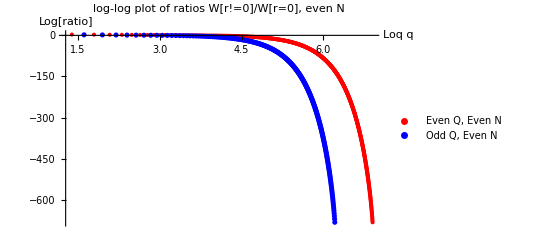

```mathematica
Show[PlotEE,PlotOE, 
PlotLabel->"log-log plot of ratios W[r!=0]/W[r=0], even N",
AxesLabel->{"Loq q", "Log[ratio]"}
]
```

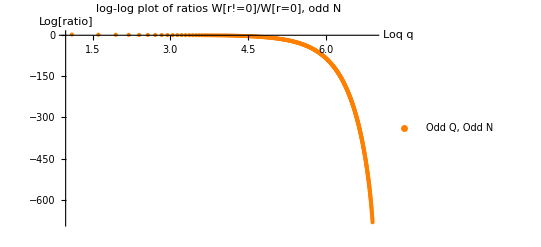

```mathematica
Show[PlotOO, 
PlotLabel->"log-log plot of ratios W[r!=0]/W[r=0], odd N",
AxesLabel->{"Loq q", "Log[ratio]"}
]
```

```mathematica
ZZeven[N_]:= (3 √2 N^(3/2))/π^(5/2);
```

```mathematica
ZZo[M_?OddQ] := Sum[N[EulerPhi[q]W[q,M],20],{q,3, M-1,2 }];
```

```mathematica
Zotable =With[{N = 10001}, ParallelTable[{M,ZZo[M]} , {M, N, N+100,2}]];
```

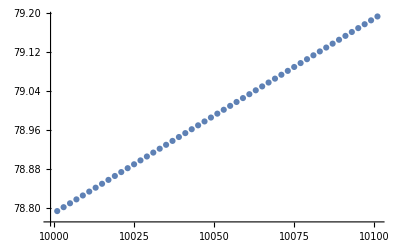

```mathematica
ListPlot[Zotable]
```

```mathematica
logmodel =LinearModelFit[Log[Zotable],{x},x]
```

FittedModel[-0.29644465713342604055+«1»]

```mathematica
Normal[logmodel]
```

-0.29644465713342604055+0.506304469015513627 x

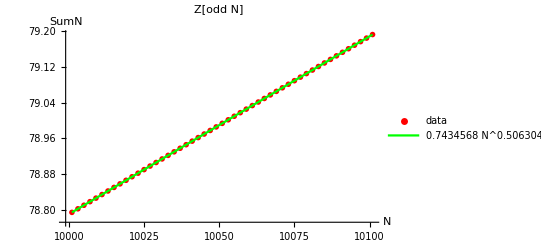

```mathematica
ShowFitLogModel[Zotable, logmodel, "Z[odd N]"]
```

```mathematica
N[logmodel["ParameterTable"],6]
```

| Estimate | Standard Error | t-Statistic | P-Value
1. | -0.296445 | 5.47956×10^-6 | -54100.1 | 3.44931×10^-192
x | 0.506304 | 5.94608×10^-7 | 851494. | 7.68323×10^-251

```mathematica
nlmodel = NonlinearModelFit[Log[Zotable],{a + b Log[x] +x/2},{a,b},x]
```

FittedModel[«1»]

```mathematica
N[nlmodel["ParameterTable"],6]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.367376 | 9.55088×10^-6 | -38465.1 | 6.25397×10^-185
b | 0.0580983 | 4.3005×10^-6 | 13509.7 | 1.15566×10^-162

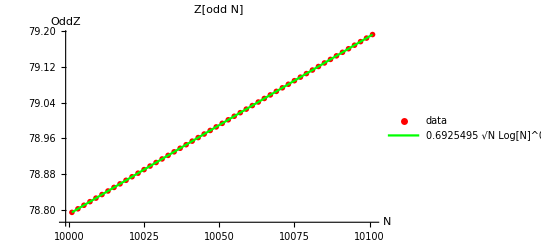

```mathematica
ShowFitLogModel[Zotable, nlmodel,"OddZ", "Z[odd N]"]
```

```mathematica
N[Exp[nlmodel[Log[N]]],5]
```

1.2072 √N Log[N]^0.078776

```mathematica
N^3 Sqrt[N]/(576 Sqrt[2 Pi] Zeta[3] (3 √2 N^(3/2))/π^(5/2))
```

(N^2 π^2)/(3456 Zeta[3])

```mathematica
Phi2[q_] := q^2 Times @@ ((1-1/#[[1]]^2) & /@ FactorInteger[q]);
```

```mathematica
Phi2[258]
```

44352

```mathematica
Z[M_]:= Sum[EulerPhi[q] W[q,M],{q,3,M-1}];
```

```mathematica
Table[Z[M],{M,4,20,1}]
```

{0,5/8,7/16,35/32,45/64,23/16,121/128,869/512,37/32,247/128,5533/4096,2193/1024,25143/16384,76619/32768,112025/65536,330809/131072,245933/131072}

```mathematica
IIevenTotal[M_?EvenQ, q_] := (2^(-5-M) (M) Gamma[1+M])/Gamma[1/2 (2+M)]^2  + IIeven[M, q];
```

```mathematica
enstrophyEven = With[{MM= 1000},ParallelTable[{M,N[Sum[IIevenTotal[M,q](Phi2[q]/3 - EulerPhi[q]),{q,3,M-1}]/Z[M],20]},{M,6,MM,2}]];
```

```mathematica
enstrophyEvenRNZ= With[{MM= 1000},ParallelTable[{M,N[Sum[IIeven[M,q](Phi2[q]/3 - EulerPhi[q]),{q,3,M-1}]/Z[M],20]},{M,5,MM,2}]];
```

```mathematica
enstrophyEvenRZ= With[{MM= 1000},ParallelTable[{M,N[(2^(-5-M) (M) Gamma[1+M])/Gamma[1/2 (2+M)]^2 Sum[(Phi2[q]/3 - EulerPhi[q]),{q,3,M-1}]/Z[M],20]},{M,6,MM,2}]];
```

```mathematica
PlotTot =ListPlot[enstrophyEven,PlotStyle->Red];
```

```mathematica
PlotRNZ =ListPlot[enstrophyEvenRNZ,PlotStyle->Green];
```

```mathematica
PlotRZ =ListPlot[enstrophyEvenRZ,PlotStyle->Blue];
```

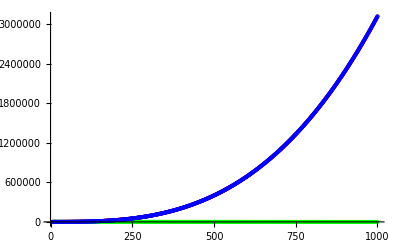

```mathematica
Show[PlotTot,PlotRNZ, PlotRZ, PlotLegends->{"Total", "r !=0", "r ==0"}]
```

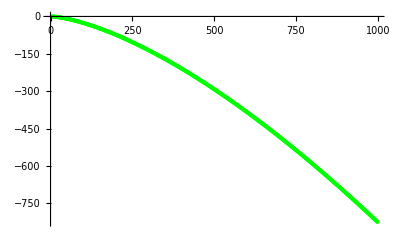

```mathematica
Show[PlotRNZ, PlotLegends->{ "r !=0"}]
```

```mathematica
enstrophyEven[[;;10]]
```

{{6,0.58035714285714285714},{8,1.4907407407407407407},{10,3.1766528925619834711},{12,6.0109797297297297297},{14,9.9691434724983432737},{16,15.177584218271487094},{18,22.273291118054005802},{20,30.76166747311937262},{22,40.810252858316923718},{24,53.684392345916079858}}

```mathematica
enstrophyEvenRZ[[;;10]]
```

{{6,0.89285714285714285714},{8,2.2037037037037037037},{10,4.2846074380165289256},{12,7.511402027027027027},{14,11.849900596421471173},{16,17.446307123254981506},{18,24.942027449230082571},{20,33.845163960645107949},{22,44.324836977009368115},{24,57.646210570673768954}}

```mathematica
enstrophyOdd = With[{MM= 1001},ParallelTable[{M,N[Sum[IIodd[M,q](Phi2[q]/3 - EulerPhi[q]),{q,3,M-1,2}]/Z[M],20]},{M,5,MM,2}]];
```

```mathematica
PlotTotOdd =ListPlot[enstrophyOdd,PlotStyle->Red];
```

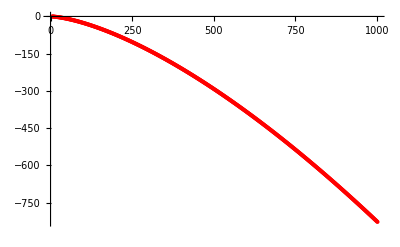

```mathematica
Show[PlotTotOdd, PlotLegends->{ "Odd N"}]
```

```mathematica
ZdataOdd = With[{MM= 1001},ParallelTable[{M,N[Z[M],20]},{M,5,MM,2}]];
```

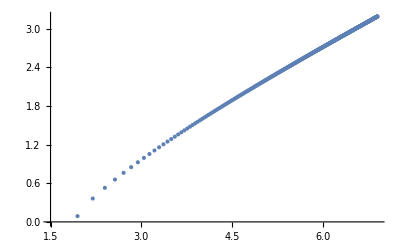

```mathematica
ListPlot[Log[ZdataOdd]]
```

```mathematica
Integrate[(3 √2 N^(3/2))/π^(5/2)E^(-μ N),{N,0,Infinity},GenerateConditions->False]
```

9/(2 √2 π^2 μ^(5/2))

```mathematica
AA =Integrate[N^3 Sqrt[N]E^(-μ N),{N,0,Infinity},GenerateConditions->False];
BB = 576 Sqrt[2 Pi] Zeta[3]Integrate[(3 √2 N^(3/2))/π^(5/2)E^(-μ N),{N,0,Infinity},GenerateConditions->False];
```

```mathematica
FullSimplify[AA/BB, μ >0]
```

(35 π^2)/(13824 μ^2 Zeta[3])

```mathematica
enstrophyOdd = With[{MM= 2001},ParallelTable[{M,-N[Sum[IIodd[M,q](Phi2[q]/3 - EulerPhi[q]),{q,3,M-1,2}],20]},{M,5,MM,2}]];
```

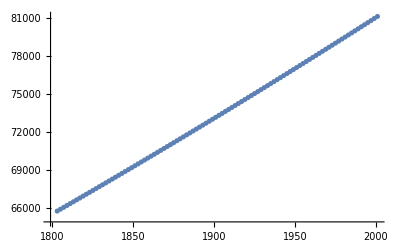

```mathematica
ListPlot[enstrophyOdd[[-100;;]]]
```

```mathematica
logmodOdd = LinearModelFit[Log[enstrophyOdd[[-100;;]]],{x, Log[x]},x]
```

FittedModel[-4.46391090942605829414+«59» x+«59» Log[x]]

```mathematica
Normal[logmodOdd]
```

-4.46391090942605829414+1.9558120192560788249 x+0.444196141095153414082 Log[x]

```mathematica
N[logmodOdd["ParameterTable"],5]
```

| Estimate | Standard Error | t-Statistic | P-Value
1. | -4.4639 | 0.00012141 | -36768. | 2.6012×10^-348
x | 1.9558 | 0.000015743 | 124230. | 1.3334×10^-399
Log[x] | 0.4442 | 0.00011885 | 3737.3 | 5.3357×10^-252

```mathematica
Exp[logmodOdd[Log[N]]]
```

0.00249173599432981704 N^1.634320871694260931 Log[N]^2.389773750232931803

```mathematica
N[Zeta[3]]
```

1.20206

```mathematica
logmodOdd[N]/.Log[N]-> Log[1/μ]
```

-4.46391090942605829414+1.9558120192560788249 N+0.444196141095153414082 Log[1/μ]

```mathematica
Integrate[Exp[logmodOdd[Log[N]]]Exp[-μ N],{N,1,Infinity}]
```

∫_1^∞ 0.011517232241141373236 ⅇ^(-N μ) N^1.9558120192560788249 Log[N]^0.444196141095153414082ⅆN

```mathematica
N[-Integrate[(Exp[logmodOdd[Log[N]]]/.Log[N]-> Log[1/μ])Exp[-μ N],{N,0,Infinity},GenerateConditions->False]/(9/(2 √2 π^2 μ^(5/2))),5]
```

-(0.068618 Log[1/μ]^0.4442)/μ^0.45581

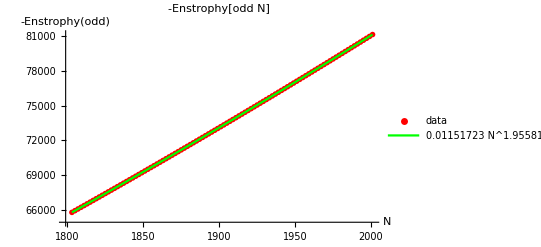

```mathematica
ShowFitLogModel[enstrophyOdd[[-100;;]], logmodOdd,"-Enstrophy(odd)", "-Enstrophy[odd N]"]
```